## Lenguajes y Gramáticas

## Lenguaje

```mathematica
(* poder mejorar la comunicación entre el ordenador y el ser humano, un ejemplo son los compiladores *)
```

## Gramática

```mathematica
(* Letras mayusculas para simbolos no terminales, letras minusculas para simbolos terminales, simbolo no terminal inicial, es la S mayuscula *)
```

```mathematica
(* P corresponde a las reglas gramaticales *)
```

```mathematica
(* el asterísco en un conjunto, como en este caso, lo que hace referencia es a todas las hileras que se pueden construir a partir de ese abecedario *)
```

```mathematica
(* este último es como el estado inicial de un automata *)
```

```mathematica
(*------------------------------------------------------------*)
```

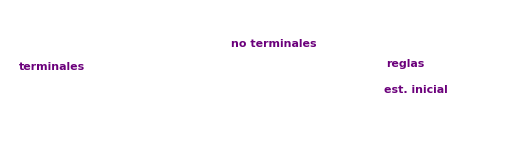
```mathematica
-Graphics--Graphics-
```

```mathematica
(* un elemento de un lenguaje no debe de estar compuesto por símbolos no terminales, siempre deben de ser terminales *)
(* una hilera siempre debe de estar compuesta po símbolos terminales *)
```

```mathematica
(* Proceso de derivación: *)
(* Siempre se parte por S *)
```

```mathematica
(* El lenguaje de una gramática va ser el conjunto de todas las hileras de símbolos terminales que puedan ser derivados partiendo de S (estado inicial) a partir de las reglas, producciones o composiciones dadas *)
```

```mathematica
(*--------------------------------------------------------------------------------------------*)
```

```mathematica
(* ElementoLenguajeQ solo se puede usar cuando la gramatica es libre del contexto *)
(* libre del contexto: que todas las reglas gramaticales, parten de UN símbolo NO terminal *)
```

```mathematica
ElementoLenguajeQ[{"S->aA|aB","A->aC","B->Dc","C->bC|b","D->c|Dc"},"aabbbbbb"]
```

True

```mathematica
(* Para verificar todas las hileras: *)
```

```mathematica
Hileras={"aabbbbbb","accccccc","aabbbccc"};
(* Se ponen las derivaciones dentro de un vector *)
Table[ElementoLenguajeQ[{"S->aA|aB","A->aC","B->Dc","C->bC|b","D->c|Dc"},α],{α,Hileras}]
```

```mathematica
(* Es necesario tener cuidado cuando da el resultado false, el comando realiza como maximo 30 derivaciones, y podria pasar que con las 30 derivaciones resultara insuficiente y se ocuparan mas, y aun asi devolveria falso *)
```

{True,True,False}

```mathematica
(* Asi que se utiliza la opcion pruebas: *)
```

```mathematica
Table[ElementoLenguajeQ[{"S->aA|aB","A->aC","B->Dc","C->bC|b","D->c|Dc"},i,pruebas->50],{i,Hileras}]
```

{True,True,False}

```mathematica
(* usualmente se usa cuando la gramatica es libre del contexto *)
```

```mathematica
(* los símbolos no terminales se ponen entre simb de mayor menos, y las flechas se cambian por ::= y si hay algún símbolo no terminal que deriva a más de uno terminal o no terminal, se pone con | *)
```

```mathematica
NotationBNF[{"S->aA|aB","A->aC","B->Dc","C->bC|b","D->c|Dc"}]
```

<S>::=a<A>|a<B>

<A>::=a<C>

<B>::=<D>c

<C>::=b<C>|b

<D>::=c|<D>c

σ^*=S

```mathematica
NotationFNormal[{"S->aA|aB","A->aC","B->Dc","C->bC|b","D->c|Dc"}]
```

Símbolos no terminales: {A,B,C,D,S}

Símbolos terminales: {a,b,c}

Producciones o reglas de composición: {A→aC,B→Dc,C→b,C→bC,D→c,D→Dc,S→aA,S→aB}

σ^*=S

```mathematica
(*------------------------------------------------------------------*)
```

## Clasificación de Gramáticas

```mathematica
(* alfa -> es UN símbolo no terminal  *)
(* gama y delta -> hileras de símbolos no terminales y/o terminales pudiendo ser la hilera vacía *)
(* beta -> es una hilera de símbolos no terminales y/o terminales pero excluyendo a la hilera vacía *)
```

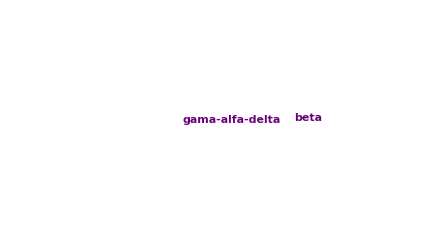
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Las gramaticas regulares son las que se pueden convertir a automatas, no se necesitarian derivaciones *)
```

```mathematica
(* Toda gramatica regualar va ser libre *)
(* Toda gramatica regualar que no contenga a una hilera vacia, es sensible *)
(* Hay gramaticas que no son ni libres, regulares o sensibles *)
(* Para ser regular debe de tener un simbolo no terminal a terminal no terminal, o no terminal a terminal *)
```

```mathematica
(* Para que sea regular las reglas deben de tener esta forma: *)
(* NT -> T NT *)
(* NT -> T  *)
```

```mathematica
(* En el ejemplo 8.2, la gramatica no es regular pero sí sería libre de contexto, todas parten de nodos no terminales *)
```

```mathematica
(* Los simbolos terminales serian . Roberto Maria astudia examina problemas siempre frecuentemente b *)
```

```mathematica
(* Cuantas posibles oraciones se podrian hacer: 8, la gramatica tiene 8 elementos, es finito *)
```

```mathematica
ElementosLenguaje[{"S->AbB.","A->r|m","B->CbDbE","C->e|x","D->p","E->s|f"},6,8] 
(* Longitud máxima de 8, obtenidos por a lo sumo 6 derivaciones, sobre una gramática libre del contexto, posee la opción derivaciones->True *)
```

{mbebpbf.,mbebpbs.,mbxbpbf.,mbxbpbs.,rbebpbf.,rbebpbs.,rbxbpbf.,rbxbpbs.}

```mathematica
(*-------------------------------------------------------------------------------------------*)
```

Símbolos no terminales:
S: real
A: real con signo
B: real sin signo
C: parte real
D: entero sin signo
E: parte decimal
F: dígito

Símbolos terminales: -, ., 0, 1, 2, 3, 4, 5, 6, 7, 8, 9

```mathematica
ElementoLenguajeQ[{"S->A|B","A->-C","B->C","C->D|0E|DE","E->.D","D->F|FD","F->0|1|2|3|4|5|6|7|8|9"},"-123.654"]
```

True

```mathematica
(*----------------------------------------------------------------*)
```

```mathematica
(* es regular *)
(* es más simple convertir la gramática a un autómata para así determinar su lenguaje más fácilmente *)
```

```mathematica
(* **** Si tengo reglas que va de un símbolo no terminal a uno terminal, eso lo que indica es que ese va ser el estado aceptado **** *)
```

Estados: {A,EA,S}

Símbolos de entrada: {a,b}

Estado inicial: S

Estados aceptados: {EA}

(  | a | b
A | {} | {A,EA}
EA | {} | {}
S | {A} | {S})

Función de transición de estados con otro formato: {{A,a,{}},{A,b,{A,EA}},{EA,a,{}},{EA,b,{}},{S,a,{A}},{S,b,{S}}}

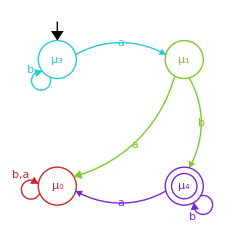

```mathematica
RegularToAutomata[{"S->bS|aA","A->bA|b"},colores->True,dfa->True]
```

```mathematica
(* *** Imp: dfa->True convierte el automata no derterministico equivalente a uno deterministico equivalente *)
```

```mathematica
(*----------------------------------------------------------------*)
```

```mathematica
(* Este autómata es equivalente a la gramática, tienen el mismo lenguaje, así que las hileras aceptadas por el autómata serían el lenguaje de la gramática *)
```

```mathematica
(* EA es el estado aceptado, va ser solamente un estado aceptado *)
```

```mathematica
(* Para saber si una gramatica es regular y libre de contexto *)
```

```mathematica
gramatica={"S->aS|bA|b","A->aA|a|bB","B->aS|bA|b"};
```

```mathematica
{GramaticaRegularQ[gramatica],GramaticaLibreContextoQ[gramatica]}
```

{True,True}

```mathematica
(*-----------------------------------------------------------*)
```

```mathematica
(* Para pasar de un automata regular a un automata no determinisitico *)
(* Si se pone dfa->True el diagrama del automata seria deterministico *)
```

Estados: {A,B,EA,S}

Símbolos de entrada: {a,b}

Estado inicial: S

Estados aceptados: {EA}

(  | a | b
A | {A,EA} | {B}
B | {S} | {A,EA}
EA | {} | {}
S | {S} | {A,EA})

Función de transición de estados con otro formato: {{A,a,{A,EA}},{A,b,{B}},{B,a,{S}},{B,b,{A,EA}},{EA,a,{}},{EA,b,{}},{S,a,{S}},{S,b,{A,EA}}}

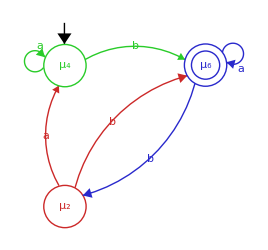

```mathematica
RegularToAutomata[gramatica,colores->True,dfa->True]
```

```mathematica
(*------------------------------------------------------------------------*)
```

```mathematica
(* sirve para crear un autómata det. a partir del lenguaje dado, y a partir de eso. convertirlo a grámatica, y así diseñar la gramática *)
```

```mathematica
(* Para el primero: abb *)
```

```mathematica
(* Para el segundo: *)
```

```mathematica
(* Ahora, con el software: *)
```

```mathematica
Clear[A]
```

```mathematica
aut=Automata[{S,A,B},{a,b},S,{{S,a,A},{S,b,S},{A,a,B},{A,b,A},{B,a,B},{B,b,B}},{B}]
```

- Automaton -

```mathematica
(* Para ver el diagrama: *)
```

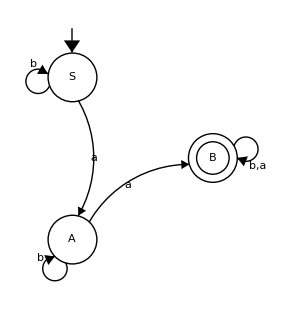

```mathematica
AutomataToDiagrama[aut]
```

```mathematica
AutomataToRegular[aut]
```

Símbolos no terminales: {S,A,B}

Símbolos terminales: {a,b}

Producciones o reglas de composición: {A→a,A→aB,A→bA,B→a,B→aB,B→b,B→bB,S→aA,S→bS}

σ^*=S